```mathematica
SetDirectory[NotebookDirectory[]]
data=Import["data.xlsx"][[1]][[3;;13,4;;5]]
```

C:\Users\alexn\OneDrive\GitHub\Labs\Physics_Labs\6_sem\Lab6113

{{0.00337724,8.51719},{0.00329511,8.22684},{0.00323394,7.95156},{0.00317088,7.60589},{0.00312617,7.47307},{0.00307882,7.22984},{0.00302911,7.00307},{0.00298463,6.88755},{0.00293789,6.75693},{0.00288917,6.60665},{0.00285535,6.49224}}

```mathematica
dataFit=LinearModelFit[data,x,x]
```

FittedModel[-4.93196+3973.19 x]

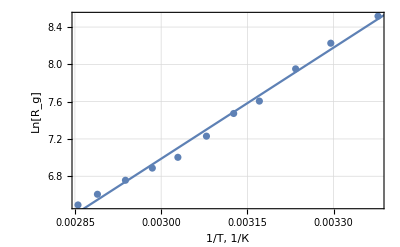

```mathematica
plot=Show[ListPlot[data,PlotTheme->"Detailed",FrameLabel->{"1/T, 1/К","Ln[R_g]"}],Plot[dataFit["BestFit"],{x,0,1}]]
```

```mathematica
Export["plot.pdf",plot]
```

plot.pdf

```mathematica
k=dataFit["BestFitParameters"][[2]];
k=Quantity[k,"Kelvins"]
```

3973.19 K

```mathematica
ScientificForm[k]
```

3.97319×10^3 K

```mathematica
kb=Quantity[1,"BoltzmannConstant"];
e=Quantity[1,"ElementaryCharge"];
```

```mathematica
ΔV=kb/e k
```

3973.19 K k/e

```mathematica
UnitConvert[ΔV,"Volts"]
```

0.342383 V